### Homework Problems #4, Graphing.

#### #1.

Graph the following functions on the same axis.

ⅇ^x
1
x+1
x^2/2+x+1
x^3/6+x^2/2+x+1
x^4/24+x^3/6+x^2/2+x+1

Include plot labels. Comment on the pattern that you see developing, and comment on why this might be the case.

{ⅇ^x,1,1+x,1+x+x^2/2,1+x+x^2/2+x^3/6,1+x+x^2/2+x^3/6+x^4/24}

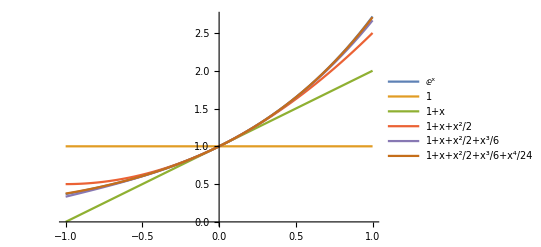

```mathematica
functions = Prepend[Accumulate[{1,x,x^2/2, x^3/6, x^4/24}], ⅇ^x]
Plot[functions,{x,-1,1},PlotLegends->"Expressions"]
```

Successive functions approximate e^x because the formula $\sum_{n=0}^\infty \frac{x^n}{n!}$ is the definition of e. So taking the first few terms results in a decent approximation around x=0.

#### #2.

Graph the two ellipses whose equations are given below. How many points of intersection are there?

```mathematica
1/4 (x-1)^2+y^2==1
(x-2)^2+1/4 (y-2)^2==1
```

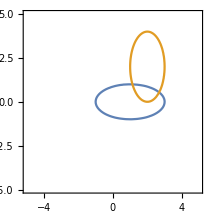

```mathematica
f1=(1/4) (x-1)^2 + y^2;
f2 = (x-2)^2 + (1/4) (y-2)^2;
ContourPlot[{f1 == 1, f2 == 1},{x,-5,5},{y,-5,5}]
```

There are two points of intersection.

#### #3.

Similar to the random walk in 2 dimensions given in today’s notes, create a random walk constrained to the lattice. That is, the only allowable moves are to move one unit west, east, north, or south. The function RandomChoice will come in handy here. An example output is

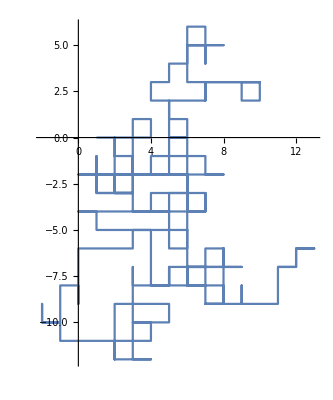

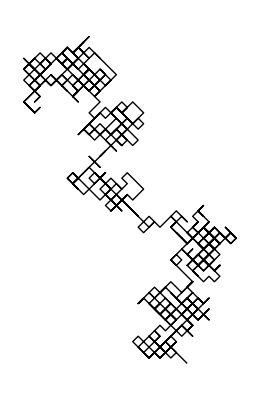

```mathematica
SeedRandom[01011999];(*seed with my birthday*)
walk=RandomFunction[RandomWalkProcess[0.5],{0,10^3},2];
Graphics[Line[Transpose@walk["ValueList"]],AspectRatio->Automatic]
```

#### #4.

Write a function called plotSwitchXY that returns a plot of a given equation, along with the plot of the same equation with the roles of x and y reversed. For example

```mathematica
plotSwitchXY[x^2-x^4,{x,-3,3}]
```

should return a plot that looks like

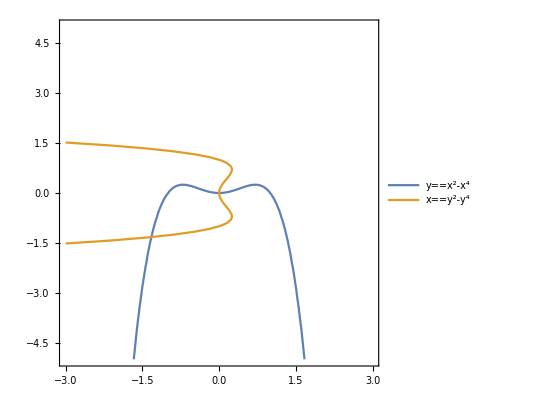

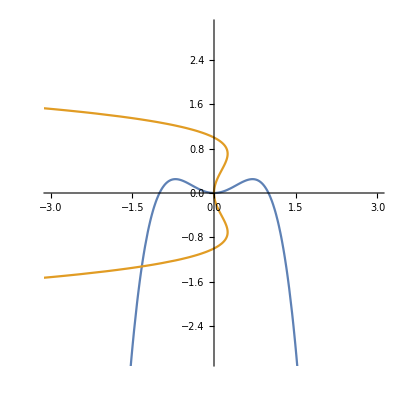

```mathematica
plotSwitchXY[f_,range_]:=ParametricPlot[{{u,f/.x->u},{f/.x->u,u}},{u,-10,10}, PlotRange->{{range[[2]],range[[3]]},{range[[2]],range[[3]]}}]
plotSwitchXY[x^2-x^4,{x,-3,3}]
```

### #5.

Plot the torus  with equation  (Sqrt[x^2+y^2]-2)^2 +z^2 =1 together with a curve on the torus which wraps 20 times around the circle x^2+y^2=4 while traveling once around the z-axis. (This should be familiar.)

```mathematica
Clear["Global`*"]
torus=ContourPlot3D[(Sqrt[x^2+y^2]-2)^2 + z^2 == 1,{x,-4,4},{y,-4,4},{z,-4,4}];
R=2;r=1;m=20;
curve=ParametricPlot3D[
{Cos[20t](R-r Cos[t]),
Sin[20t](R-r Cos[t]),
r Sin[t]},
{t,0, 2π}
];
Show[torus,curve](*I'm pretty sure I'm interpreting this correctly...*)
```

-Graphics3D-

#### #6.

A de Bruijn graph is a directed graph representing overlaps between sequences of symbols. There is a built in function called DeBruijnGraph that creates such a graph. By using the options GraphLayout, EdgeShapeFunction, VertexLabels, VertexSize, and VertexStyle, see if you can replicate a figure such as the following. The plot underlying this figure was DeBruijnGraph[4,2]. The vertex sizes were chosen at random.

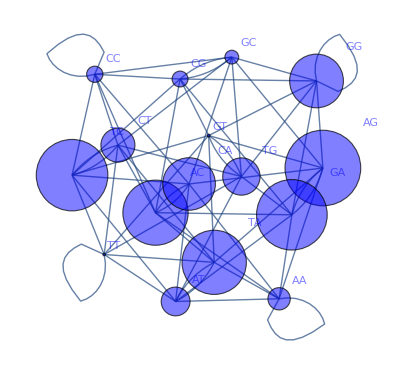

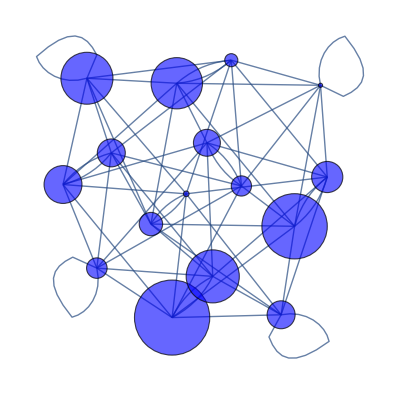

```mathematica
Clear["Global`*"]
DeBruijnGraph[4,2, 
GraphLayout->"SpringElectricalEmbedding", EdgeShapeFunction->"Line",
VertexLabels->"",
VertexSize->Thread[Range[Length[DeBruijnSequence[4,2]]]->RandomReal[1.8,Length[DeBruijnSequence[4,2]]]],
VertexStyle->Opacity[0.6,Blue]]
```

This is as close as I can get. I know it’s possible to use EdgeLabels to label the appropriate edges, but I’m really not sure how to get them to work as in the image. It’s something I’d have to read more into the function options and what they all do. It was hard enough to get it to this point :).